# Teoremas de unicidad y existencia

## Campos de pendientes y condiciones iniciales

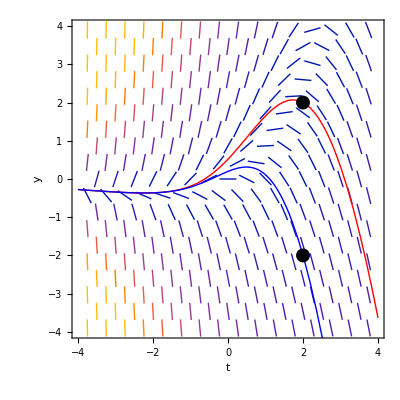

```mathematica
Show[VectorPlot[{1,2*Exp[-t/2]*y-t},{t,-4,4},{y,-4,4},FrameLabel->{t,y},VectorStyle->Arrowheads[0]],Plot[Evaluate[y[t]/.sol1],{t,-4,4},PlotStyle->{Red,Thick}],Plot[Evaluate[y[t]/.sol2],{t,-4,4},PlotStyle->{Blue,Thick}],Graphics[{PointSize[0.025],Point[{2,2}]}],Graphics[{PointSize[0.025],Point[{2,-2}]}]]
```

```mathematica
sol1=NDSolve[{y'[t]==2*Exp[-t/2]*y[t]-t,y[2]==2},y,{t,-4,4}];
sol2=NDSolve[{y'[t]==2*Exp[-t/2]*y[t]-t,y[2]==-2},y,{t,-4,4}];
```

## Ejemplo I

Ecuación original:

En la forma usual:

Es lineal con  y , sólo podemos garantizar existencia y unicidad de las soluciones para  ó .
La solución particular con condiciones iniciales  es 

Vemos que la solución no existe en . Su intervalo de existencia es .
Esta expresión también es solución para las condiciones iniciales , pero su intervalo de existencia es .
Podemos visualizar estas dos soluciones distintas (dadas por la misma expresión) en el campo de pendientes:

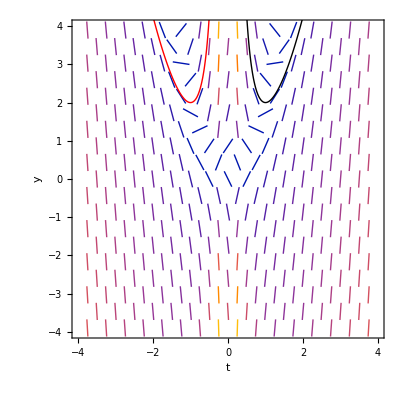

```mathematica
Show[VectorPlot[{1,4*t-2*y/t},{t,-4,4},{y,-4,4},FrameLabel->{t,y},VectorStyle->Arrowheads[0]],Plot[t^2+t^(-2),{t,1/4,2},PlotStyle->{Black,Thick}],Plot[t^2+t^(-2),{t,-2,-1/4},PlotStyle->{Red,Thick}]]
```

## Ejemplo II

Ecuación:

Es no lineal con  y derivada parcial . Son continuas en todo R excepto en .
Con condiciones iniciales  tenemos la solución , la cual existe siempre que lo que está dentro de la raíz no sea negativo. Cuando es cero, tenemos , es decir, deja de existir justo en el punto donde no podemos garantizar la existencia.
Con condiciones iniciales  la solución es , vemos que la solución no es única, hay dos funciones diferentes que satisfacen el problema con condiciones iniciales.

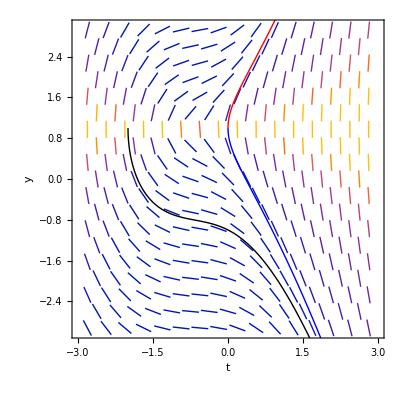

```mathematica
Show[VectorPlot[{1,(3*t^2+4*t+2)/(2*y-2)},{t,-3,3},{y,-3,3},FrameLabel->{t,y},VectorStyle->Arrowheads[0]],Plot[1-Sqrt[t^3+2*t^2+2*t+4],{t,-2,2},PlotStyle->{Black,Thick}],Plot[1+Sqrt[t^3+2*t^2+2*t],{t,0,3},PlotStyle->{Red,Thick}],Plot[1-Sqrt[t^3+2*t^2+2*t],{t,0,3},PlotStyle->{Blue,Thick}]]
```

## Ejemplo III

Ecuación diferencial:

Condiciones iniciales:

La ecuación es no lineal, y ,  son continuas en todo R.
Solución general :

Solución particular:

La solución sólo existe en el intervalo , aun cuando el teorema de existencia y unicidad se cumple para todo R.

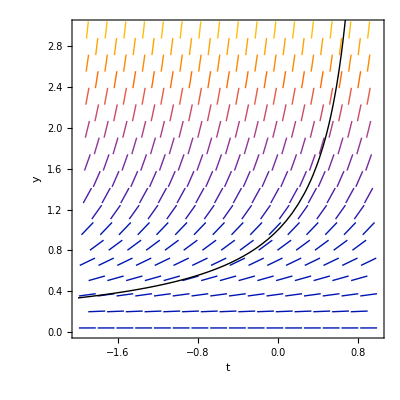

```mathematica
Show[VectorPlot[{1,y^2},{t,-2,1},{y,0,3},FrameLabel->{t,y},VectorStyle->Arrowheads[0]],Plot[1/(1-t),{t,-2,1},PlotStyle->{Black,Thick}]]
```